```mathematica
dpdt=-gammapn[t]*np[t]+gammanp[t]*nn[t]
dndt=+gammapn[t]*np[t]-gammanp[t]*nn[t]
x[t]=nn[t]/np[t]
ye[t_]:=1/(1+x[t])
dyedt=FullSimplify[D[ye[t],t]//.{ nn'[t]->dndt,np'[t]->dpdt}]
dyedt=FullSimplify[dyedt//.{nn[t]->xnew[t]*np[t]}]
dyedt=FullSimplify[dyedt//.{xnew[t]->(1-yenew[t])/yenew[t]}]
```

gammanp[t] nn[t]-gammapn[t] np[t]

-gammanp[t] nn[t]+gammapn[t] np[t]

nn[t]/np[t]

(gammanp[t] nn[t]-gammapn[t] np[t])/(nn[t]+np[t])

(-gammapn[t]+gammanp[t] xnew[t])/(1+xnew[t])

gammanp[t]-(gammanp[t]+gammapn[t]) yenew[t]

```mathematica
(* OLD *)
D[1/(1+x),x]
np=nn/x
dndt=np*gampe-nn*(gamne+gamn)
dpdt=-dndt
dxdt=FullSimplify[x*(1/nn*dndt-1/np*dpdt)]
dyedt = FullSimplify[-1/(1+x)^2*dxdt]
FullSimplify[dyedt//.{x->1/ye-1}]
```

-1/(1+x)^2

nn/x

-(gamn+gamne) nn+(gampe nn)/x

(gamn+gamne) nn-(gampe nn)/x

(1+x) (gampe-(gamn+gamne) x)

(-gampe+(gamn+gamne) x)/(1+x)

gamn+gamne-(gamn+gamne+gampe) ye

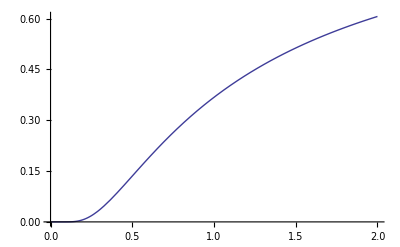

```mathematica
Plot[Exp[-1/x],{x,0,2}]
```

```mathematica
Exp[-1/(10^(-6.))]
```

3.29683148×10^-434295

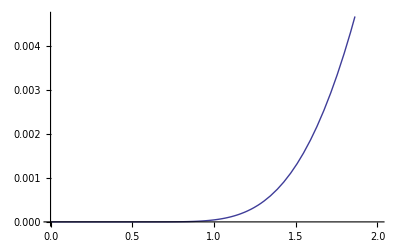

```mathematica
Plot[Exp[-10/x],{x,0,2}]
```

```mathematica
Exp[-10/30.]
```

0.716531

```mathematica
xtot = (x/(1+x)*xnuc+2*mpomalpha*(1-xnuc))/(1/(1+x)*xnuc+2*mpomalpha*(1-xnuc))
mynpratio=FullSimplify[Solve[yetot == 1/(1+xtot),x]]
```

(2 mpomalpha (1-xnuc)+(x xnuc)/(1+x))/(2 mpomalpha (1-xnuc)+xnuc/(1+x))

{{x→-1-xnuc/(-xnuc yetot+2 mpomalpha (-1+xnuc) (-1+2 yetot))}}

```mathematica
mynpratio//.{xnuc->.15,mpomalpha->.25,yetot->0.43}
```

{{x→29.}}

```mathematica
thermalnpratio=gammap2n/gamman2p
thermalye = FullSimplify[1/(1+thermalnpratio)]
```

gammap2n/gamman2p

gamman2p/(gamman2p+gammap2n)